```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=p^2/(2m)(*p^2/(2m)*);Nx=5;max=100;
```

```mathematica
m =50/2;λ=π/2;
```

```mathematica
Clear@α
```

```mathematica
α=(*0.33375*)0.474;
```

```mathematica
ϕ[α_?NumberQ][n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[α_?NumberQ][n_][p_?NumberQ]:=ω[p]ϕ[α][n][p]-λ/π NIntegrate[(ϕ[α][n][k]-ϕ[α][n][p]-(k-p)ϕ[α][n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
H1[α_?NumberQ][n_][p_?NumberQ]:=ω[p]ϕ[α][n][p]
H2[α_?NumberQ][n_][p_?NumberQ]:=-λ/π NIntegrate[(ϕ[α][n][k]-ϕ[α][n][p]-(k-p)ϕ[α][n]'[p])/(p-k)^2,{k,-max,0,max}]
```

```mathematica
findgrnene[α_?NumberQ]:=First@Sort@Eigenvalues@Table[If[Abs[i-n]≤1,NIntegrate[ϕ[α][2i][p]H1[α][2n][p],{p,-max,max},MaxRecursion->10],0]+2NIntegrate[ϕ[α][2i][p]H2[α][2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]
```

```mathematica
FindMinimum[findgrnene[α],{α,0.5},StepMonitor:>Print@{α,findgrnene[α]}]//AbsoluteTiming
```

{0.486235,0.370492}

{0.390612,0.369154}

{0.352173,0.368952}

{0.304591,0.368825}

{0.265388,0.368777}

{0.235357,0.368764}

{0.231502,0.368764}

{0.233101,0.368764}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{23700.,{0.368764,{α→0.233101}}}

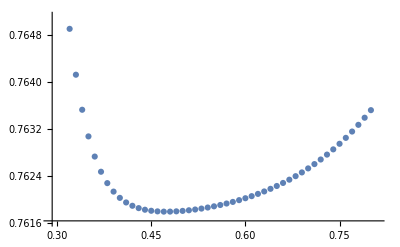

```mathematica
ListPlot[αen=Table[{α,findgrnene[α]},{α,0.3,0.8,0.01}]]
```

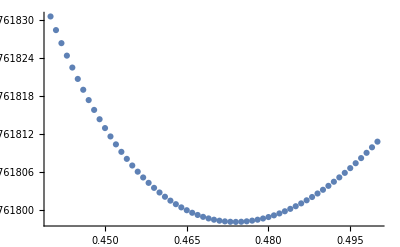
{13089.,-Graphics-}

```mathematica
ListPlot[αen=Table[{α,findgrnene[α]},{α,0.44,0.5,0.001}]]//Timing
```

```mathematica
Last[%7]
```

-Graphics-

```mathematica
αen
```

{{0.44,0.761831},{0.441,0.761828},{0.442,0.761826},{0.443,0.761824},{0.444,0.761823},{0.445,0.761821},{0.446,0.761819},{0.447,0.761817},{0.448,0.761816},{0.449,0.761814},{0.45,0.761813},{0.451,0.761812},{0.452,0.76181},{0.453,0.761809},{0.454,0.761808},{0.455,0.761807},{0.456,0.761806},{0.457,0.761805},{0.458,0.761804},{0.459,0.761803},{0.46,0.761803},{0.461,0.761802},{0.462,0.761801},{0.463,0.761801},{0.464,0.7618},{0.465,0.7618},{0.466,0.7618},{0.467,0.761799},{0.468,0.761799},{0.469,0.761799},{0.47,0.761798},{0.471,0.761798},{0.472,0.761798},{0.473,0.761798},{0.474,0.761798},{0.475,0.761798},{0.476,0.761798},{0.477,0.761798},{0.478,0.761798},{0.479,0.761799},{0.48,0.761799},{0.481,0.761799},{0.482,0.761799},{0.483,0.7618},{0.484,0.7618},{0.485,0.761801},{0.486,0.761801},{0.487,0.761801},{0.488,0.761802},{0.489,0.761803},{0.49,0.761803},{0.491,0.761804},{0.492,0.761804},{0.493,0.761805},{0.494,0.761806},{0.495,0.761807},{0.496,0.761807},{0.497,0.761808},{0.498,0.761809},{0.499,0.76181},{0.5,0.761811}}

```mathematica
findgrnene[0.5]
```

0.761811

```mathematica
Table[2NIntegrate[ϕ[0.5][2i][p]H[0.5][2n][p],{p,0,max},MaxRecursion->10],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
Sort@Eigenvalues[Last[%]]
```

{181.306,{{0.778467,0.103774,-0.138219,-0.0370295,-0.0375651,-0.0225352},{0.117919,2.52588,0.352224,-0.207555,-0.0231149,-0.04256},{-0.138216,0.386881,3.7148,0.528185,-0.272903,-0.0140929},{-0.0370295,-0.207542,0.582997,4.69135,0.672486,-0.331806},{-0.0375651,-0.0231149,-0.272875,0.747394,5.54231,0.797115},{-0.0225352,-0.04256,-0.0140929,-0.331759,0.892103,6.30717}}}

{0.761811,2.35927,3.44314,4.4756,5.65685,6.86329}

```mathematica
2NIntegrate[ϕ[0.5][0][p]H[0.5][0][p],{p,0,max},MaxRecursion->50]//Timing
```

{2.35938,0.778467}

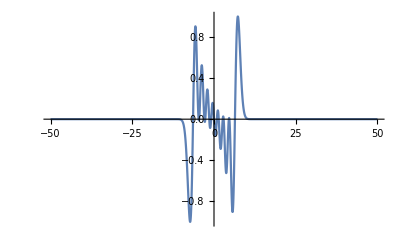

```mathematica
Plot[ϕ[6][p]H[9][p],{p,-50,50},PlotRange->All]
```